```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"];
```

```mathematica
α=1.0;
β=3.0;
γ=1.0;
rc=20(*kpc*);
rsun=8.5(*kpc*);
ρsun=0.3(*Gev/cc*);
```

```mathematica
ρ[r_]:=ρsun(rsun/r)^γ((rc^α+rsun^α)/(rc^α+r^α))^((β-γ)/α)
```

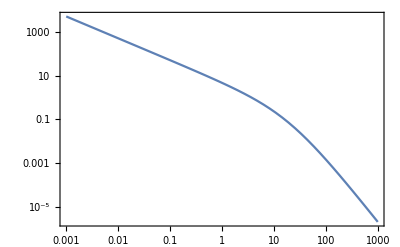

```mathematica
LogLogPlot[ρ[r],{r,0.001,1000},PlotRange->Full,Frame->True]
```

```mathematica
ρ[7.7]
```

0.350574